```mathematica
HERMITE
```

HERMITE

```mathematica
data= Import["E:\\Alessio\\Desktop\\Computazionale\\es7\\data_hermite.txt","Table"];
DELTAHermite = Take[data][[All,{1,3}]]
```

{{2,935.62022925103906345611903816461563110351563},{4,844.9619842363640600524377077817916870117188},{5,559.153800777849596670421306043863296508789063},{8,1.5870638137016612745355814695358276367188×10^-13},{100,1.5870638137016612745355814695358276367188×10^-13}}

```mathematica
LAGUERRE
```

LAGUERRE

```mathematica
data= Import["E:\\Alessio\\Desktop\\Computazionale\\es7\\data_laguerre.txt","Table"];
DELTALaguerre = Take[data][[All,{1,3}]]
```

{{2,721.30576606535964856448117643594741821289063},{3,98.075985886950476810852705966681241989135742188},{4,0.4791563224607220949913255481078522279858589172363},{5,0.02115872164149595890947352927469182759523391723633},{6,0.002622652739160458157385846789111383259296417236328},{7,0.0005289691595867229700900224997894838452339172363281},{8,0.0001432464357098983676053194358246400952339172363281},{9,0.00004738578259139147874634545587468892335891723632813},{10,0.00001813314652326925013881009363103657960891723632813},{12,3.62030602946150636967104219365864992141723632813×10^-6},{14,9.6477476790868266220968507695943117141723632813×10^-7},{16,3.1406621064933304410260461736470460891723632813×10^-7},{20,5.000465580495827566664956975728273391723632813×10^-8},{32,1.16376713821253474634431768208742141723632813×10^-9},{64,5.63932234243225138925481587648391723632813×10^-12}}

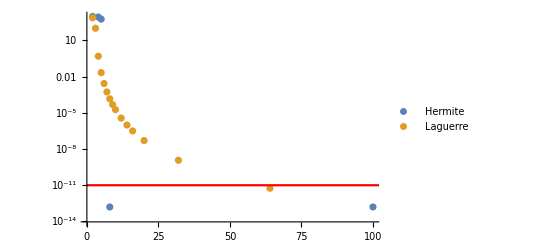

```mathematica
Show[{ListLogPlot[{DELTAHermite,DELTALaguerre},PlotLegends->{"Hermite", "Laguerre"}, PlotRange->All],LogPlot[10^(-11),{x,0,110},PlotStyle->Red]}]
```

```mathematica
g[x_]= x^14 * E^(-x^2) 
min = 0
max = Infinity
```

ⅇ^(-x^2) x^14

0

∞

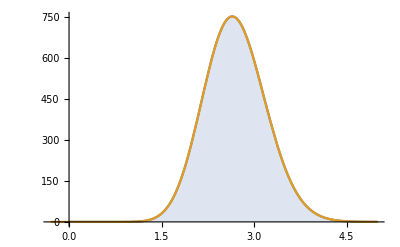

```mathematica
Plot[{If[min<x<max, g[x]],g[x]},{x,min-0.3,5}, Filling->{1->Axis}]
```

```mathematica
Integrate[g[x],{x,0,Infinity}]
N[%]
```

(135135 √π)/256

935.627

```mathematica
f[y_]:=NIntegrate[g[x],{x,2,y}]
```

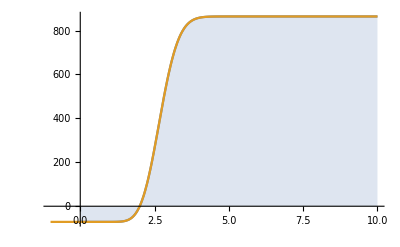

```mathematica
Plot[{If[min<x<max, f[x]],f[x]},{x,min-1,10}, Filling->{1->Axis}]
```

```mathematica
Integrate[0.5*(Log[x]^2),{x,0,E^(-9)}]
```

0.0062322